```mathematica
/Users/warren/Documents/Princeton/EGR191/Lab 7/Mathematica Code
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[(M2/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+33.7402 t-1. gt t}}

-0.199024+33.7402 t-1. gt t

-0.199024 t+16.8701 t^2-0.5 gt t^2

33.7402-1. gt

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]}}

-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]

-0.199024 t-0.5 gt t^2-13.0384 t^2 Log[1.45159 (0.6889-1. M0t)]

-1. gt-26.0768 Log[1.45159 (0.6889-1. M0t)]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0*t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-0.5 gt t^2-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-1. gt-26.0768/(1.-2.68309 t)+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

{{v[t]→-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

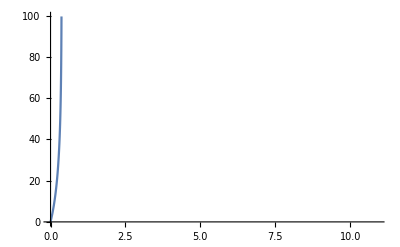

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-4.85947 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

340000.

0.0000708822

0.6889

9.81

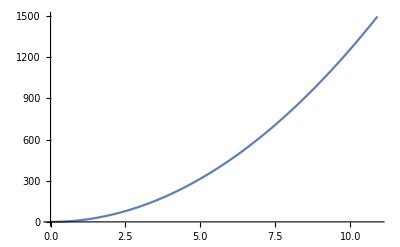

```mathematica
Clear[P1,A1,M1,g,u,M0]

sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]

P1=3.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81

Plot[h1[t],{t,0,10.91}]
```

{{v[t]→-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])}}

-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])

-1.635 t^3-(0.34445 t u)/M0+0.75 t^2 u-(0.237292 u Log[1.-1.45159 M0 t])/M0^2+(0.6889 t u Log[1.-1.45159 M0 t])/M0-0.5 t^2 u Log[1.-1.45159 M0 t]

-1/M04.905 (2. M0 t-0.203874 M0 u+(0.203874 M0 u)/(1.-1.45159 M0 t)-(0.295941 M0^2 t u)/(1.-1.45159 M0 t)+0.203874 M0 u Log[1.-1.45159 M0 t])

26.0768

0.1889

0.6889

1.84838

9.81

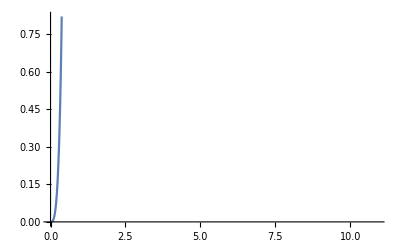

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[h2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

k=ρ2*A2/2
C=0.1
A2=((.06)^2)*Pi

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

0.00689894

0.1

0.0113097

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
```

NDSolve[{V'[t]==0.0130371 pi √(-100000+2 P0 (V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
```

NDSolve[{V'[t]==0.375506 pi √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},v[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},v[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {V'[t]==0.0000708822 √((-P2+2 Power[«2»] P0 Power[«2»])/ρ2),False}.

NDSolve[{V'[t]==0.0000708822 √((-P2+2 0.0015^g P0 (1/V[t])^g)/ρ2),False},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,1,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,1,4}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(gamma)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
gamma=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^gamma (1/V[t])^gamma),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^g1 (1/V[t])^g1),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.000181239 (1/V[t])^(5/14),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M-ρ1*ve*A*t),v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

{{v[t]→(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve}}

(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve

(680. t)/ve+(680. t Log[M])/ve+(9593.38 M Log[1. M-0.0708822 t ve])/ve^2-(680. t Log[1. M-0.0708822 t ve])/ve

48.1999/(1. M-0.0708822 t ve)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

```mathematica
Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ClearAll
```

ClearAll

{{v[t]→-(9.81 (1. t ve ρ1-69317. Log[M0]+0.203874 P2 Log[M0]+69317. Log[M0-1. A t ve ρ1]-0.203874 P2 Log[M0-1. A t ve ρ1]))/(ve ρ1)}}

-(9.81 (1. t ve ρ1-69317. Log[M0]+0.203874 P2 Log[M0]+69317. Log[M0-1. A t ve ρ1]-0.203874 P2 Log[M0-1. A t ve ρ1]))/(ve ρ1)

-4.905 t^2+(680000. t)/(ve ρ1)-(2. P2 t)/(ve ρ1)+(680000. t Log[M0])/(ve ρ1)-(2. P2 t Log[M0])/(ve ρ1)+(680000. M0 Log[M0-1. A t ve ρ1])/(A ve^2 ρ1^2)-(2. M0 P2 Log[M0-1. A t ve ρ1])/(A ve^2 ρ1^2)-(680000. t Log[M0-1. A t ve ρ1])/(ve ρ1)+(2. P2 t Log[M0-1. A t ve ρ1])/(ve ρ1)

-(9.81 (1. ve ρ1-(69317. A ve ρ1)/(M0-1. A t ve ρ1)+(0.203874 A P2 ve ρ1)/(M0-1. A t ve ρ1)))/(ve ρ1)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

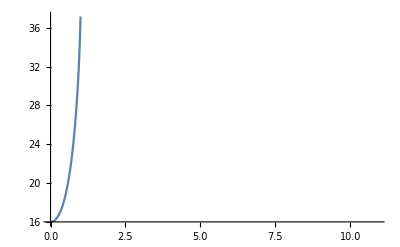

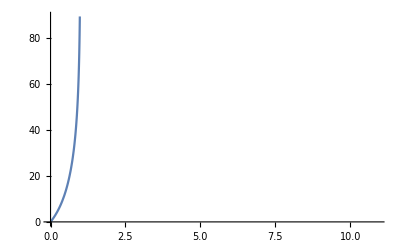

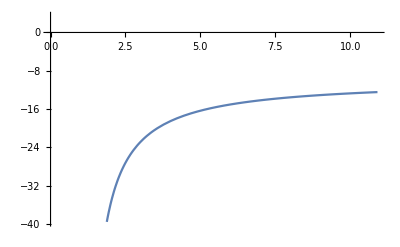

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi

Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v1^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v1=26.07680962
```

DSolve[{0==9.81-0.0365216 C v1^2,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M_2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M_2=.1889
ve=26.07680962
```

DSolve[{0==9.81-(2.34564 C)/M_,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

```mathematica
C
```

C

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
x=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 x,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

-Graphics-

-Graphics-

-Graphics-

```mathematica
C =
```

```mathematica
ve
```

26.0768

```mathematica
x
```

0.5

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{False,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{False,26.0768[0]==0}

∫(26.0768[t]/.{False,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{False,26.0768[0]==0})

```mathematica
ClearAll
```

ClearAll

```mathematica
ve
```

26.0768

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ve
```

26.0768

```mathematica
v
```

26.0768

```mathematica
Clear["Global`*"]
```

```mathematica
v
```

v

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.8
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962
```

{{v[t]→(g M2 t-C k t ve^2)/M2}}

(g M2 t-C k t ve^2)/M2

1/2 t^2 (g-(C k ve^2)/M2)

(g M2-C k ve^2)/M2

9.8

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→9.8 t-24.8347 C t}}

9.8 t-24.8347 C t

4.9 t^2-12.4174 C t^2

9.8-24.8347 C

```mathematica
c
```

c

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
c = 1
```

1

```mathematica
c
```

1

```mathematica
c = .1
```

0.1

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→7.31653 t}}

7.31653 t

3.65826 t^2

7.31653

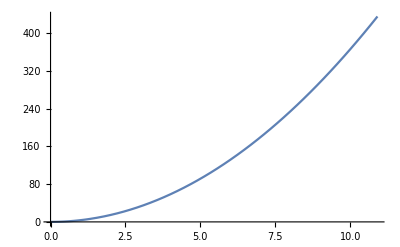

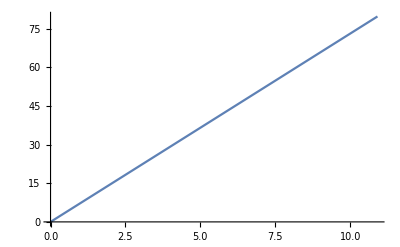

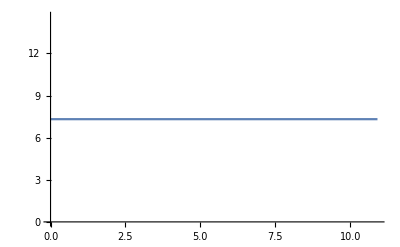

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==(k*c*(ve)^(2))/(M2)-g,v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→-7.31653 t}}

-7.31653 t

-3.65826 t^2

-7.31653

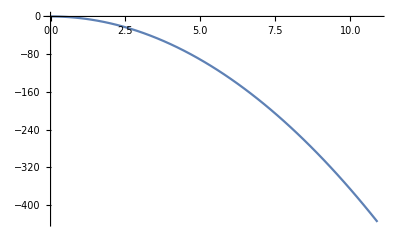

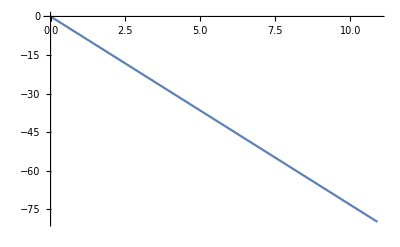

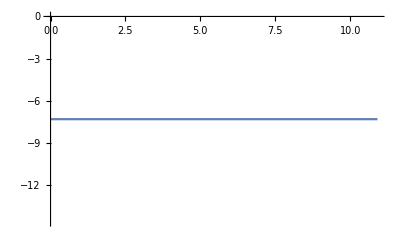

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*v^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

DSolve[{v'[t]==9.8+0.00365216 v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*(ve)^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

{{v[t]→12.2835 t}}

12.2835 t

6.14174 t^2

12.2835

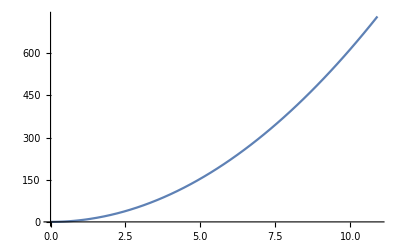

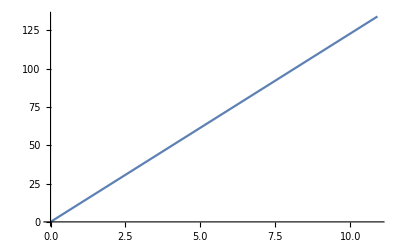

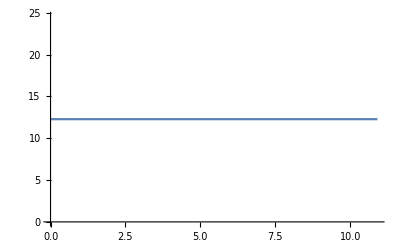

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.5
M2=.1889
ve=26.07680962
```

DSolve[{v'[t]==9.8-0.00365216 v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.8-0.00365216 v^2,v[0]==0})

9.81

1.22

```mathematica
Clear
```

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]

P1=3.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

340000.

0.0000708822

0.6889

9.81

```mathematica
Clear[g,k,c,M2]
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]== v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]


g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.1
M2=.1889
v0=30
ve=26.07680962


Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

```mathematica
h3[t]
```

54.7621 Log[Cos[0.423248 t-ArcTan[0.0431445 v0]]]

9.81

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(23.1779 (-1.+1. ⅇ^(0.846495 t)))/(1.+1. ⅇ^(0.846495 t))}}

-(23.1779 (-1.+1. ⅇ^(0.846495 t)))/(1.+1. ⅇ^(0.846495 t))

23.1779 t-54.7621 Log[1.+ⅇ^(0.846495 t)]

```mathematica
(19.620000000000005 ⅇ^(0.84649544751168 t) (-1.+1. ⅇ^(0.84649544751168 t)))/((1.+1. ⅇ^(0.84649544751168 t))^2)-(19.620000000000005 ⅇ^(0.84649544751168 t))/(1.+1. ⅇ^(0.84649544751168 t))
Clear[g,k,c,M2]
```

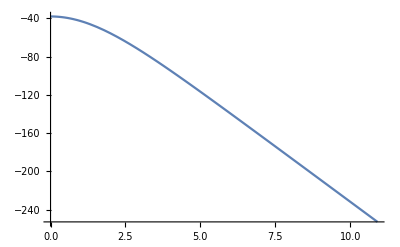

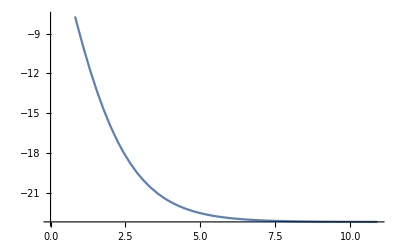

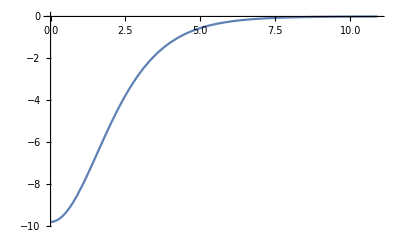

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==g-(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

-51.8274 t+273.81 Log[1.+ⅇ^(0.378564 t)]

-(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)+(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.1
M2=.1889
ve=26.07680962
```

9.81

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
c
```

0.12

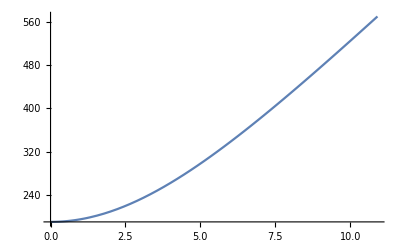

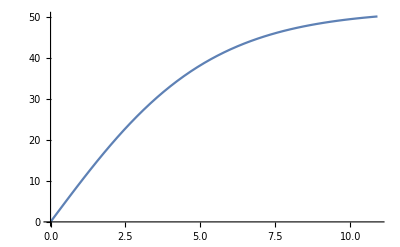

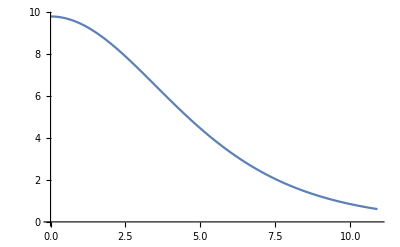

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==vsol1[t1]},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→-245.201-9.81 t-26.0768 Log[0.0000708822-1. A t]}}

-245.201-9.81 t-26.0768 Log[0.0000708822-1. A t]

-219.124 t-4.905 t^2+(0.00184838 Log[0.0000708822-1. A t])/A-26.0768 t Log[0.0000708822-1. A t]

-9.81+(26.0768 A)/(0.0000708822-1. A t)

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==vsol2[t2]},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(51.8274 (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)}}

(51.8274 (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)

(t (-2.20181×10^17-2.16186×10^16 Log[0.000262035-1. A])+(2.64156 (1.14067×10^33+2.95683×10^32 Log[0.000262035-1. A]+1.80353×10^31 Log[0.000262035-1. A]^2) Log[4.24836×10^15-2.59029×10^15 ⅇ^(0.378564 t)+(4.17126×10^14-4.17126×10^14 ⅇ^(0.378564 t)) Log[0.000262035-1. A]])/(2.59029×10^15+4.17126×10^14 Log[0.000262035-1. A]))/(4.24836×10^15+4.17126×10^14 Log[0.000262035-1. A])

-(19.62 ⅇ^(0.378564 t) (1. ⅇ^(0.378564 t)-1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.))/((1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)^2)+(19.62 ⅇ^(0.378564 t))/(1. ⅇ^(0.378564 t)+1. ((-4.79373×10^15-4.17126×10^14 Log[0.0000708822-0.270507 A])/(3.13566×10^15+4.17126×10^14 Log[0.0000708822-0.270507 A]))^1.)

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→18.3238 Tan[0.535371 t]}}

18.3238 Tan[0.535371 t]

-34.2263 Log[Cos[0.535371 t]]

9.81 Sec[0.535371 t]^2

```mathematica
P1=4.4*10^5
P2=10^5
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
M0=1.8483812
M1=0.6889
M2=.1889
g=9.81
ρ1=1000
ρ2=1.22
k=ρ2*A2/2
```

440000.

100000

0.0000708822

0.0113097

1.84838

0.6889

0.1889

9.81

1000

1.22

0.00689894

```mathematica
c=0.1

v0=30
ve=26.07680962
t1=0.1113732799
t2=0.2705069712
t3=vsol2[t2]
t4=10.91
```

0.1

30

26.0768

0.111373

0.270507

0.0000556659 (311055.-468452. Log[1.84838-7053.96 A])

10.91

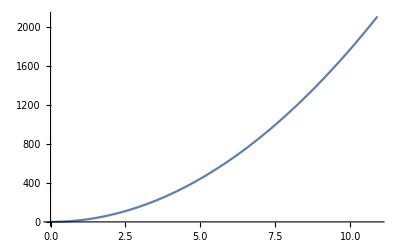

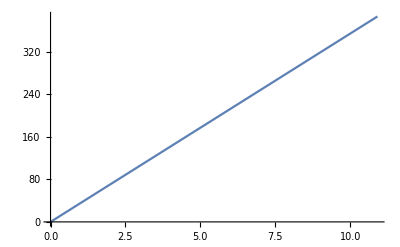

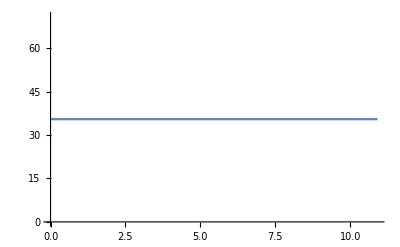

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

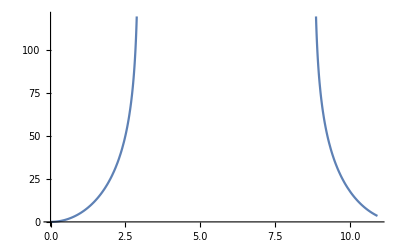

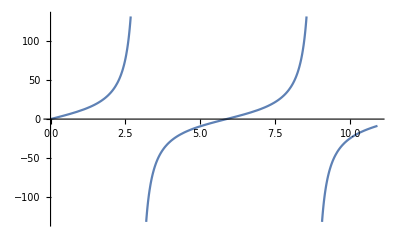

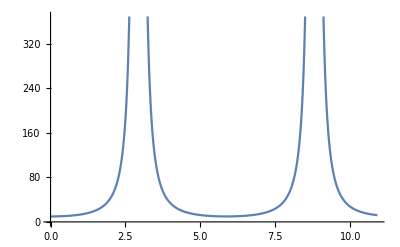

```mathematica
Plot[h1[t],{t,0,10.91}]
Plot[vsol1[t],{t,0,10.91}]
Plot[a1[t],{t,0,10.91}]

Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]

Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

```mathematica
P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81

Plot[h1[t],{t,0,10.91}]
Plot[vsol1[t],{t,0,10.91}]
Plot[a1[t],{t,0,10.91}]
```

440000.

0.0000708822

0.6889

9.81

-Graphics-

-Graphics-

-Graphics-

```mathematica
t1 =Solve[h1[t] == .22, t]
```

{{t→-0.111389},{t→0.111389}}

```mathematica
vsol1[t1]
t
```

{{35.4624 (t→-0.111389)},{35.4624 (t→0.111389)}}

```mathematica
t
Clear[t]
```

t

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

440000.

100000

26.0768

0.1889

0.6889

1.84838

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==35.46240683482751},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

{{v[t]→35.4624-9.81 t-26.0768 Log[1.-1. t]}}

35.4624-9.81 t-26.0768 Log[1.-1. t]

61.5392 t-4.905 t^2+26.0768 Log[1.-1. t]-26.0768 t Log[1.-1. t]

-9.81+26.0768/(1.-1. t)

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

440000.

100000

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

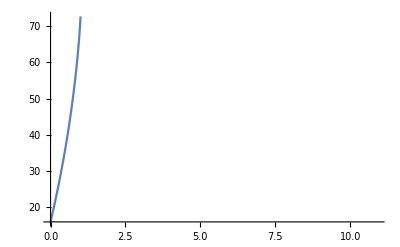

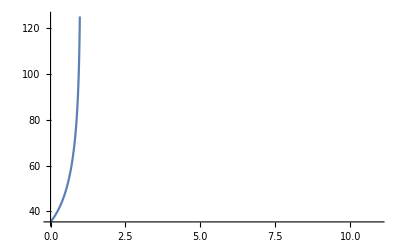

-Graphics-

```mathematica
Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

```mathematica
vsol2[.27]
```

41.0204

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]=v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of v0 in the first argument {v'[t]==g-(c k v[t]^2)/M2,v0}.

DSolve[{v'[t]==g-(c k v[t]^2)/M2,v0},v[t],t]

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0}

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {g==(c k (Integrate`Y)^2)/M2+v'[t],v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

∫(v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0})ⅆt

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,v0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{v'[t]==g-(c k v[t]^2)/M2,v0})

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {v'[t]==g-(c k v[t]^2)/M2,True}.

DSolve[{v'[t]==g-(c k v[t]^2)/M2,True},v[t],t]

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True}

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {g==(c k (Integrate`Y)^2)/M2+v'[t],True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

∫(v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True})ⅆt

ReplaceAll::reps: {v'[t]==g-(c k v[t]^2)/M2,True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{v'[t]==g-(c k v[t]^2)/M2,True})

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tanh[(√c √g √k t+√M2 ArcTanh[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

```mathematica
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)])/(√c √k)

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k v0)/(√g √M2)]]])/(c k)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k v0)/(√g √M2)])/(√M2)]^2

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

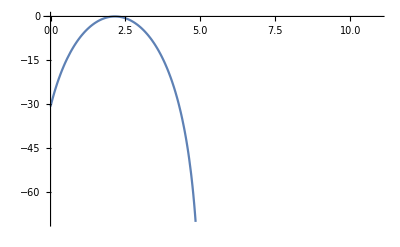

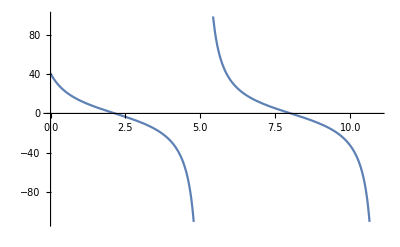

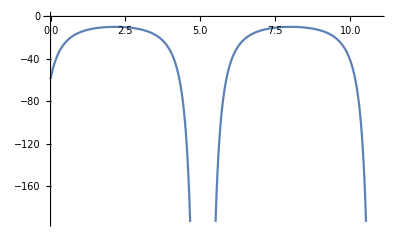

```mathematica
Clear[g,k,c,v0]
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(v[t])^(2))/(M2),v[0]==v0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
tsol3 = Solve[h3[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→1684.05 √M2 Tanh[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]}}

1684.05 √M2 Tanh[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]

289097. M2 Log[Cosh[(0.00582523 t)/(√M2)+1. ArcTanh[(0.000593805 v0)/(√M2)]]]

9.81 Sech[(1.75968×10^-13 (3.31039×10^10 t+5.68285×10^12 √M2 ArcTanh[(0.000593805 v0)/(√M2)]))/(√M2)]^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.-171.667 √M2 ArcTanh[(0.000593805 v0)/(√M2)]}}

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

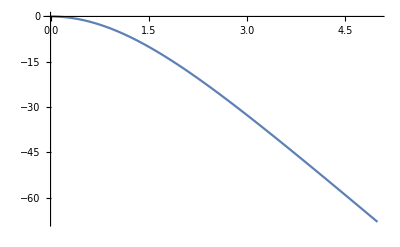

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]
```

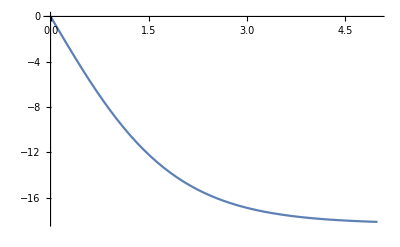

```mathematica
Plot[vsol4[t],{t,0,5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))}}

-(18.3238 (-1.+1. ⅇ^(1.07074 t)))/(1.+1. ⅇ^(1.07074 t))

18.3238 t-34.2263 Log[1.+ⅇ^(1.07074 t)]

(19.62 ⅇ^(1.07074 t) (-1.+1. ⅇ^(1.07074 t)))/((1.+1. ⅇ^(1.07074 t))^2)-(19.62 ⅇ^(1.07074 t))/(1.+1. ⅇ^(1.07074 t))

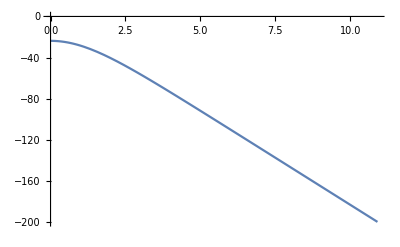

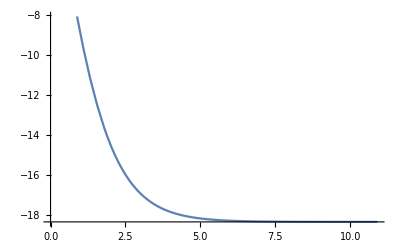

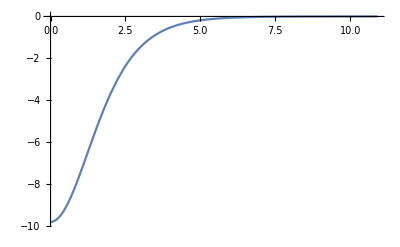

```mathematica
Plot[a4[t],{t,0,10.91}]
```

```mathematica
g Sec[(√c √g √k t)/(√M2)]^2
g=9.81
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
c=0.8
v0=41.0204
M2=.1889
ve=26.07680962
```

g Sec[(√c √g √k t)/(√M2)]^2

9.81

1.22

0.0113097

0.00689894

0.8

41.0204

0.1889

26.0768

```mathematica
Plot[h4[t],{t,0,10.91}]
Plot[vsol4[t],{t,0,10.91}]
Plot[a4[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
t1=0.111389
t2=0.2705069712
t3=
```

0.111389

0.270507

```mathematica
vcom[t_]:=vsol1[t]/;t<t1
```

```mathematica
vcom[t_]:=vsol2[t]/;t1<t<t2
```

```mathematica
vcom[t_]:=vsol3[t]/;t2<t<t3
```

```mathematica
vcom[t_]:=vsol4[t]/;t3<t<t4
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→(100000. (1. A1 t-0.0000981 M1 t))/M1}}

(100000. (1. A1 t-0.0000981 M1 t))/M1

1/2 (-9.81+(100000. A1)/M1) t^2

(100000. (1. A1-0.0000981 M1))/M1

```mathematica
Clear[L] 
Clear[v0]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]
```

{{v[t]→35.4624 t}}

35.4624 t

17.7312 t^2

```mathematica
tsol1 = Solve[h1[t]== L,t]
v0 = Simplify[vsol1[t]/.tsol1[[2]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→-0.237482 √L},{t→0.237482 √L}}

8.42169 √L

```mathematica
P1=4.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81
L=.22
```

440000.

0.0000708822

0.6889

9.81

0.22

```mathematica
Plot[h1[t],{t,0,10.91}]

Plot[vsol1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

{{t→-0.111389},{t→0.111389}}

0.111389

```mathematica
vsol1[t]
```

35.4624 t

```mathematica
Clear[vsol1,tsol1]
```

```mathematica
vsol1
```

```mathematica
vsol1
v0
```

vsol1

8.42169 √L

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t)-g,v[0]==v0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]
```

```mathematica
M[t]==M0-A*ve*1000*t
```

```mathematica
M[t]==M0-1.848381224048865 t

tsol2=Solve[M[t]==0,t]
v1=Simplify[vsol2[t]/.tsol2[[2]]]
```

M[t]==M0-1.84838 t

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→M^(-1)[0]}}

Part::partw: Part 2 of {{t→M^(-1)[0]}} does not exist.

ReplaceAll::reps: {{{t→M^(-1)[0]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

3.95012-9.81 t-26.0768 Log[1.-1. t]/.{{t→M^(-1)[0]}}⟦2⟧

```mathematica
Clear[M0]
```

```mathematica
P1=4.4*10^5
P2=10^5
ve=26.07680962
M0=.1889
M1=.6889
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
L=.22
```

440000.

100000

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

0.22

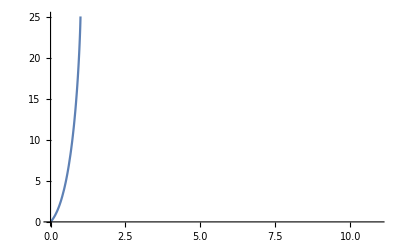

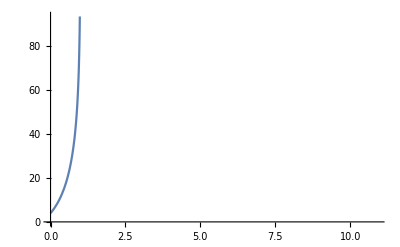

-Graphics-

```mathematica
Plot[h2[t],{t,0,10.91}]

Plot[vsol2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]
```

```mathematica
M[t]==M0-A*ve*1000*t
```

M[t]==1.84838-1.84838 t